```mathematica
dir=NotebookDirectory[];
```

```mathematica
input=Import[dir<>"../data/"<>"01.txt"]
```

08, 23, 09, 00, 12, 11, 01, 10, 13, 07, 41, 04, 14, 21, 05, 17, 03, 19, 02, 06

```mathematica
x=Interpreter["Integer"]/@StringSplit[input,","]
```

{8,23,9,0,12,11,1,10,13,7,41,4,14,21,5,17,3,19,2,6}

```mathematica
MinFree1[xs_]:=First@Complement[Range[0,Length@xs],xs]
```

```mathematica
MinFree1@x
```

15

```mathematica
SeedRandom@88;rx=Table[Drop[Range[0,(3^i)],{RandomInteger[3^i-1]}],{i,6,12}];
```

```mathematica
MinFree1/@rx
```

{255,1503,5841,11880,56150,113679,487518}

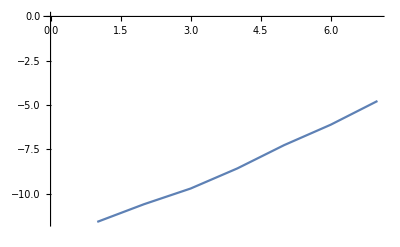

```mathematica
t1=RepeatedTiming@MinFree1[#]&/@rx//First/@#&//Log//ListPlot[#,Joined->True]&
```

```mathematica
MinFree2[xs_]:=Block[{a,n=Length@xs,ix=xs+1},
a=ConstantArray[0,n];
ix=Select[ix,#≤n&];
a[[ix]]=1;
First@FirstPosition[a,0]-1
]
```

```mathematica
MinFree2@x
```

15

```mathematica
MinFree2/@rx
```

{255,1503,5841,11880,56150,113679,487518}

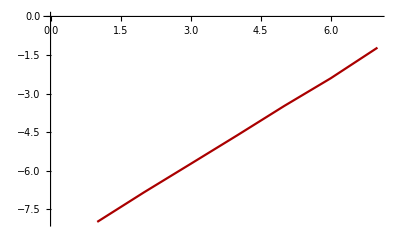

```mathematica
t2=RepeatedTiming@MinFree2[#]&/@rx//First/@#&//Log//ListPlot[#,Joined->True,PlotStyle->Darker@Red]&
```

```mathematica
PartitionB[xs_,b_]:={Select[xs,#<b&], Select[xs,#≥b&]}
```

```mathematica
PartitionB[x,10]
```

{{8,9,0,1,7,4,5,3,2,6},{23,12,11,10,13,41,14,21,17,19}}

```mathematica
MinFrom[a_,{n_,xs_}]:=Block[{b=a+1+Quotient[n,2],us,vs,m},
{us,vs}=PartitionB[xs,b];
m=Length@us;
Which[
n==0, a,
m==b-a,MinFrom[b,{n-m,vs}],
True,MinFrom[a,{m,us}]]
]
```

```mathematica
MinFree3[xs_]:=MinFrom[0,{Length@xs,xs}]
```

```mathematica
MinFree3@x
```

15

```mathematica
MinFree3/@rx
```

{255,1503,5841,11880,56150,113679,487518}

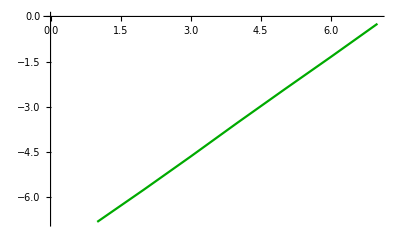

```mathematica
t3=RepeatedTiming@MinFree3[#]&/@rx//First/@#&//Log//ListPlot[#,Joined->True,PlotStyle->Darker@Green]&
```

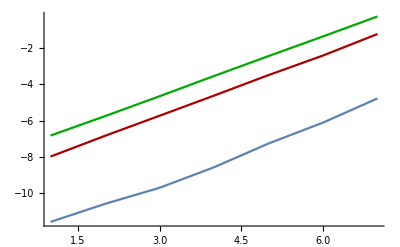

```mathematica
Show[t1,t2,t3,PlotRange->All]
```

```mathematica
RepeatedTiming@MinFree1[Last@rx]
```

{0.0072,487518}

```mathematica
RepeatedTiming@MinFree2[Last@rx]
```

{0.274,487518}

```mathematica
RepeatedTiming@MinFree3[Last@rx]
```

{0.79,487518}

```mathematica
RepeatedTiming@MinFree1@#&/@Take[rx,-2]//First/@#&//Divide@@#&
```

0.2

```mathematica
RepeatedTiming@MinFree2@#&/@Take[rx,-2]//First/@#&//Divide@@#&
```

0.3

```mathematica
RepeatedTiming@MinFree3@#&/@Take[rx,-2]//First/@#&//Divide@@#&
```

0.33

```mathematica
RepeatedTiming@MinFree1@Drop[Range[0,(4^10)],{SeedRandom@11;RandomInteger[4^10-1]}]
```

{0.019,228316}

```mathematica
RepeatedTiming@MinFree2@Drop[Range[0,(4^10)],{SeedRandom@11;RandomInteger[4^10-1]}]
```

{0.528,228316}

```mathematica
RepeatedTiming@MinFree3@Drop[Range[0,(4^10)],{SeedRandom@11;RandomInteger[4^10-1]}]
```

{1.56,228316}

```mathematica
RepeatedTiming@MinFree1@Drop[Range[0,(5^10)],{SeedRandom@11;RandomInteger[5^10-1]}]
```

{0.197,3653074}

```mathematica
RepeatedTiming@MinFree2@Drop[Range[0,(5^10)],{SeedRandom@11;RandomInteger[5^10-1]}]
```

{5.1,3653074}

```mathematica
RepeatedTiming@MinFree3@Drop[Range[0,(5^10)],{SeedRandom@11;RandomInteger[5^10-1]}]
```

{14.7,3653074}

```mathematica
RepeatedTiming@MinFree1@Drop[Range[0,(6^10)],{SeedRandom@11;RandomInteger[6^10-1]}]
```

{2.6,14612299}

```mathematica
RepeatedTiming@MinFree2@Drop[Range[0,(6^10)],{SeedRandom@11;RandomInteger[6^10-1]}]
```

{32.7,14612299}

```mathematica
RepeatedTiming@MinFree3@Drop[Range[0,(6^10)],{SeedRandom@11;RandomInteger[6^10-1]}]
```

{93.2,14612299}